```mathematica
(*To je prva opcija*)
```

```mathematica
Series[ArcCos[1-t],{t,0,7}]
```

√2 √t+t^(3/2)/(6 √2)+(3 t^(5/2))/(80 √2)+(5 t^(7/2))/(448 √2)+(35 t^(9/2))/(9216 √2)+(63 t^(11/2))/(45056 √2)+(231 t^(13/2))/(425984 √2)+O[t]^(15/2)

```mathematica
N[Series[ArcCos[1-t],{t,0,9}], 20]
```

1.4142135623730950488 √t+0.11785113019775792073 t^(3/2)+0.026516504294495532165 t^(5/2)+0.0078918167543141464777 t^(7/2)+0.0026854098677874526209 t^(9/2)+0.00098871908768538028314 t^(11/2)+0.00038344554362157376365 t^(13/2)+0.00015429118302868087157 t^(15/2)+0.000063815287098259551659 t^(17/2)+O[t]^(19/2)

1.4142135623730950488 √t+0.11785113019775792073 t^(3/2)+0.026516504294495532165 t^(5/2)+0.0078918167543141464777 t^(7/2)+0.0026854098677874526209 t^(9/2)+0.00098871908768538028314 t^(11/2)+0.00038344554362157376365 t^(13/2)+O[t]^(15/2)

1.4142135623730950488 √t+0.11785113019775792073 t^(3/2)+0.026516504294495532165 t^(5/2)+0.0078918167543141464777 t^(7/2)+0.0026854098677874526209 t^(9/2)+0.00098871908768538028314 t^(11/2)+0.00038344554362157376365 t^(13/2)+O[t]^(15/2)

```mathematica
Series[ArcCos[1-t],{t,-3,0}]
```

(-1)^(Floor[-Arg[-3-t]/(2 π)]+Floor[(π+Arg[-3-t])/(2 π)]) (ArcCos[4]+O[t+3]^1)

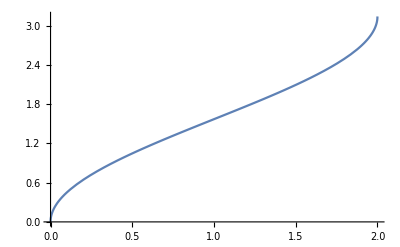

```mathematica
Plot[ArcCos[1-x],{x,0,2}]
```

```mathematica
N[1/(6*Sqrt[2]), 20]
```

0.11785113019775792073

```mathematica
1.41421356237309504880168872420969807857`20.
```

```mathematica
Series[ArcCos[1-t],{t,0,7}]
```

√2 √t+t^(3/2)/(6 √2)+(3 t^(5/2))/(80 √2)+(5 t^(7/2))/(448 √2)+(35 t^(9/2))/(9216 √2)+(63 t^(11/2))/(45056 √2)+(231 t^(13/2))/(425984 √2)+O[t]^(15/2)

```mathematica
N[3/(80 √2), 20]
```

0.026516504294495532165

```mathematica
N[5/(448 √2), 20]
```

0.0078918167543141464777

```mathematica
N[35/(9216 √2), 20]
```

0.0026854098677874526209

```mathematica
N[63/(45056 √2), 20]
```

0.00098871908768538028314

```mathematica
N[231/(425984 √2), 20]
```

0.00038344554362157376365

```mathematica
(*To je druga opcija*)
```

```mathematica
Series[ArcCos[t],{t,0,10}]
```

π/2-t-t^3/6-(3 t^5)/40-(5 t^7)/112-(35 t^9)/1152+O[t]^11

```mathematica
3/40//N
```

0.075

```mathematica
N[Series[ArcCos[t],{t,0,11}], 20]
```

1.5707963267948966192-t-0.16666666666666666667 t^3-0.075 t^5-0.044642857142857142857 t^7-0.030381944444444444444 t^9-0.022372159090909090909 t^11+O[t]^12

```mathematica
PadeApproximant[ArcCos[1-x],{x,0,4}]//Simplify
```

-((16 √2 √x (-504157610234678400+382927339061947680 x-81454890769770980 x^2+4247586091676079 x^3))/(35 (230472050392995840-194258502056306688 x+49103379054576000 x^2-3677471335540800 x^3+32162592425915 x^4)))